## Inicialize some functions

```mathematica
Remove["Global`*"]
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
```

```mathematica
(*Get["/home/strelda/Documents/programování/Mathematica/packages/GRQUICK.m"]*)
```

```mathematica
<<"/home/strelda/Documents/programování/Mathematica/packages/GRQUICK/GRQUICKv4.m"
```

The convention for this program follow Sean M. Carroll's (Spacetime and Geometry) and the indices run from 0 
to D-1.

While working do not use the variables GARRAY,RARRAY,RsARRAY, CHARRAY, SPEEDOFLIGHT.  

Type ?helpGRQUICK for a list of functions or ?Function for a function description.

More functions and improvements coming soon!!'

```mathematica
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\chi","\\lambda"},Evaluate@font,ColorFunction->"SunsetColors"};
```

## First order perturbation Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals}
```

{λ∈ℝ,χ∈ℝ}

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√((j-sn m)(j+sn m+1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4 δ[jp,j](Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2])+δ[jp,j]δ[mp,m](2j(j+1)-2m)
V2[jp_,mp_,j_,m_]:=δ[jp,j](Je[1,j,m]m δ[mp,m+1]+Je[-1,j,m]m δ[mp,m-1]+(m+1)Je[1,j,m]δ[mp,m+1]+(m-1)Je[-1,j,m]δ[mp,m-1]+2j(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1]))
V3[jp_,mp_,j_,m_]:=δ[jp,j]δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-1/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

```mathematica
jj=2;  (*jj=N/2*)
dim=2jj+1;
f[mp_,m_]:=Hd[jj,mp,jj,m]
H[χ_,λ_]=Table[f[r,z],{r,-jj,jj},{z,-jj,jj}];
```

```mathematica
If[ConjugateTranspose@H[-3,1]==H[-3,1]/.{λ-> -3,χ->1},Print["Probably is Hermitean"]]
H[χ,λ]//MatrixForm
```

Probably is Hermitean

(-2-4 λ | -χ/2 | -1/4 √(3/2) λ | 0 | 0
-χ/2 | -1+1/4 (-14 λ-χ^2) | -3/2 √(3/2) χ | -(3 λ)/8 | 0
-1/4 √(3/2) λ | -3/2 √(3/2) χ | 1/4 (-12 λ-4 χ^2) | -5/2 √(3/2) χ | -1/4 √(3/2) λ
0 | -(3 λ)/8 | -5/2 √(3/2) χ | 1+1/4 (-10 λ-9 χ^2) | -(7 χ)/2
0 | 0 | -1/4 √(3/2) λ | -(7 χ)/2 | 2+1/4 (-8 λ-16 χ^2))

## Metric tensor

### Metric tensor numerically

```mathematica
DH1[χ_,λ_]=D[H[χ,λ],λ];
DH2[χ_,λ_]=D[H[χ,λ],χ];
(*aproximatelly the same performance, maybe can be improved, but ND does not like compile functions, don't know how to fix that

gNcompile=Compile[{{λ,_Real},{χ,_Real}},
Module[{g11,g12,g22},
energies=Eigenvalues[H[λ,χ]];
g11=Re@Sum[(DH1[λ,χ][[1,i]])^2/(energies[[1]]-energies[[i]])^2,{i,2,2jj+1}]//FullSimplify;
g12=Re@Sum[(DH1[λ,χ][[1,i]]DH2[λ,χ][[1,i]])/(energies[[1]]-energies[[i]])^2,{i,2,2jj+1}]//FullSimplify;
g22=Re@Sum[(DH2[λ,χ][[1,i]])^2/(energies[[1]]-energies[[i]])^2,{i,2,2jj+1}]//FullSimplify;
{{g11,g12},{g12,g22}}
],Evaluate@compileOptions]*)
g[χ_,λ_]:=g[χ,λ]=Module[{g11,g12,g22},
energies=Eigenvalues[H[χ,λ]];
g11=Re@Sum[(DH1[χ,λ][[1,i]])^2/(energies[[1]]-energies[[i]])^2,{i,2,dim}]//FullSimplify;
g12=Re@Sum[(DH1[χ,λ][[1,i]]DH2[λ,χ][[1,i]])/(energies[[1]]-energies[[i]])^2,{i,2,dim}]//FullSimplify;
g22=Re@Sum[(DH2[χ,λ][[1,i]])^2/(energies[[1]]-energies[[i]])^2,{i,2,2jj+1}]//FullSimplify;
{{g11,g12},{g12,g22}}
]
```

#### Metric tensor determinant

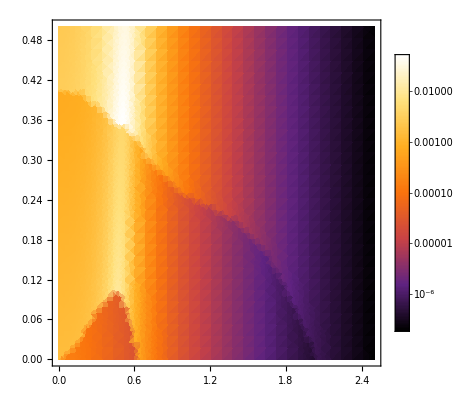

```mathematica
DensityPlot[Det[g[x,l]],{x,0,2.5},{l,0,0.5},Evaluate@densityPlotOptions,PlotPoints->30,ScalingFunctions->"Log"]
```

```mathematica
Plot3D[Det[g[x,l]],{x,0,2.5},{l,0,0.5},PlotPoints->30,ScalingFunctions->"Log",ColorFunction->"SunsetColors"]
```

-Graphics3D-

## Approximating energies

Let' s find analytical approximation for both energetic levels using Interpolation of 2 D functions.

```mathematica
gridStep=0.1;
λMax=0.5;
χMax=2.5;
```

```mathematica
eigenTab=Table[Flatten[Table[{i,j,Eigenvalues[H[i,j]][[eLevel]]},{i,0,χMax,gridStep},{j,0,λMax,gridStep}],1],{eLevel,1,dim}];
```

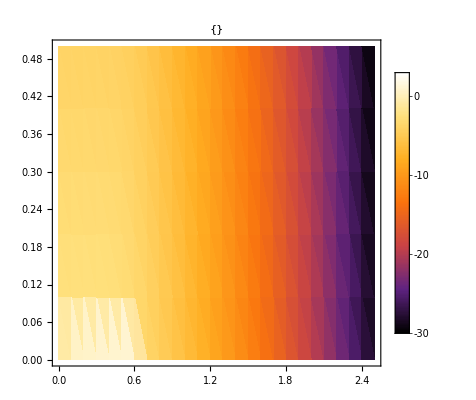

```mathematica
ListDensityPlot[eigenTab[[1]],Evaluate@densityPlotOptions,PlotLabel->MaTeX/@{"E_1"}]
```

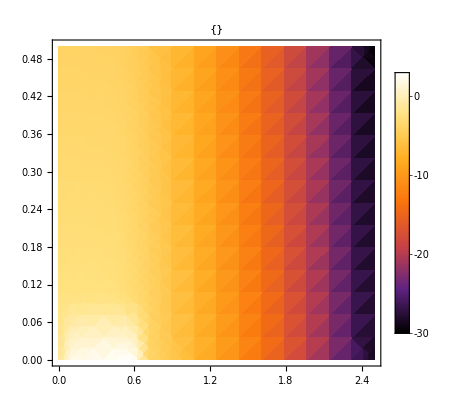

```mathematica
interp=Table[Interpolation[eigenTab[[eLevel]],InterpolationOrder->1],{eLevel,1,dim}];
DensityPlot[interp[[1]][x,y],{x,0,2.5},{y,0,0.5},Evaluate@densityPlotOptions,PlotLabel->MaTeX/@{"Interpolation E_1"}]
```

```mathematica
energies=interp;
g11[χ_,λ_]:=Sum[Re[(DH1[χ,λ][[1,i]])^2]/(energies[[1]][χ,λ]-energies[[i]][χ,λ])^2,{i,2,2jj+1}];
g12[χ_,λ_]:=Sum[Re[DH1[χ,λ][[1,i]]DH2[χ,λ][[1,i]]]/(energies[[1]][χ,λ]-energies[[i]][χ,λ])^2,{i,2,2jj+1}];
g22[χ_,λ_]:=Sum[Re[(DH2[χ,λ][[1,i]])^2]/(energies[[1]][χ,λ]-energies[[i]][χ,λ])^2,{i,2,2jj+1}];
gS[χ_,λ_]={{g11[χ,λ],g12[χ,λ]},{g12[χ,λ],g22[χ,λ]}};
```

### Difference between approximate and numerically calculated metrics

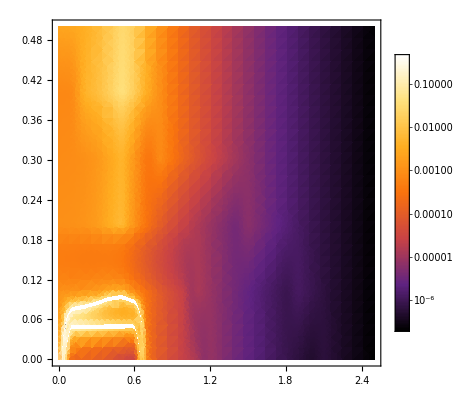

```mathematica
DensityPlot[Det[gS[χp,λp]],{χp,0,2.5},{λp,0,0.5},Evaluate@densityPlotOptions,PlotPoints->30,ScalingFunctions->"Log"]
```

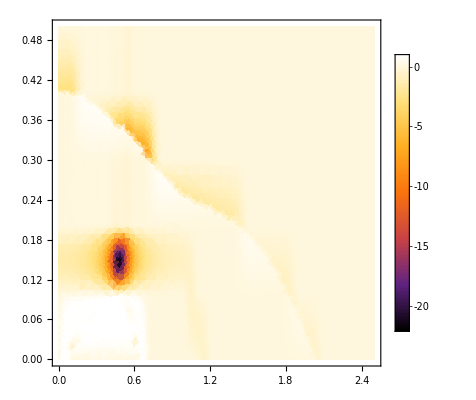

```mathematica
DensityPlot[(Det[gS[x,l]]-Det[g[x,l]])/Det[gS[x,l]],{x,0,2.5},{l,0,0.5},Evaluate@densityPlotOptions,PlotPoints->30]
```

## Finding geodesics using GRQUICK

```mathematica
Metin[gS[χ,λ],{χ,λ}]
MatrixForm[GMET]
```

Metric Success

(3/(32 (InterpolatingFunction[…][χ,λ]-InterpolatingFunction[…][χ,λ])^2) | 0
0 | 1/(4 (InterpolatingFunction[…][χ,λ]-InterpolatingFunction[…][χ,λ])^2))

```mathematica
Einstein[0,0];
Setlight[1];
geo=Geodesics[τ];
```

Now we have geo[[1]], geo[[2]] as two interpolation type functions for λ[τ], χ[τ] and the boundary value problem needs to be solved for geo[[1]]=0, geo[[2]]=0.

{0.-3.32534 ⅈ,0}

NDSolve::nlnum: The function value {0.000205297,«3»} is not a list of numbers with dimensions {4} at {τ,λ[τ],λ'[τ],χ[τ],χ'[τ]} = {6.93382×10^-8,0.1+0. ⅈ,0.000205297+0. ⅈ,0.1-2.30573×10^-7 ⅈ,2.37994×10^-7-3.32534 ⅈ}.

InterpolatingFunction::dmval: Input value {0.0000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

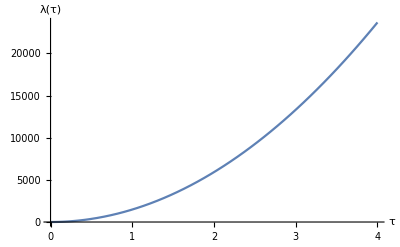
{-Graphics-,-Graphics-}

```mathematica
Setlight[1];
init={0.1,0.1};
vin={1,0};
vinit=vin/(√(-vin.GMET.vin))/.{λ->init[[1]],χ->init[[2]]}
Geoplot[τ,init,vinit,{0,4},{λ,χ}]
```

```mathematica
eqn={geo[[1]]==0,geo[[2]]==0}/.{λ->λp,χ->χp};
dirichlet={λp[0]==0.1,λp[5]==1.5,χp[0]==0.1,χp[5]==1};
cauchy[xi_,la_]:={λp[0]==0.01,λp'[0]==la,χp[0]==0.01,χp'[0]==xi};
```

```mathematica
solMulti=Table[NDSolve[Join[eqn,cauchy[Cos[θ],Sin[θ]]],{χp,λp},{τ,0,5}],{θ,0,π/2,π/15}];
```

InterpolatingFunction::dmval: Input value {0.0192296,-0.000314746} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At τ == 2.76136, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndcf: Repeated convergence test failure at τ == 0.169814; unable to continue.

NDSolve::ndsz: At τ == 2.25015, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndcf: Repeated convergence test failure at τ == 3.53415; unable to continue.

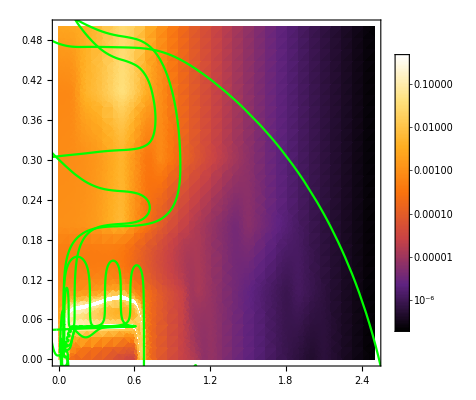

```mathematica
parp=ParametricPlot[{χp[τ],λp[τ]}/.solMulti,{τ,0,5},PlotRange->All,Frame->True,PlotStyle->Green];
denp=DensityPlot[Det[gS[χp,λp]],{χp,0,2.5},{λp,0,0.5},Evaluate@densityPlotOptions,PlotPoints->30,ScalingFunctions->"Log"];
Show[{denp,parp}]
```

```mathematica
sol=NDSolve[Join[eqn,dirichlet],{λp,χp},{τ,0,5}]
```

NDSolve::ndsz: At τ == 2.23001, step size is effectively zero; singularity or stiff system suspected.

```mathematica
parp=ParametricPlot[{χp[τ],λp[τ]}/.sol,{τ,0,5},PlotRange->All,Frame->True,PlotStyle->Green];
denp=DensityPlot[gS[χp,λp],{χp,0,2},{λp,0,3.2},Evaluate@densityPlotOptions,Exclusions->None,ClippingStyle->Automatic];
Show[{denp,parp}]
```

NDSolve::dsvar: 0.000102041 cannot be used as a variable.

## Boundary Value problem example

```mathematica
linearsystem={x'[t]==x''[t]-4*y[t]+1,y'[t]==4*x[t]+y''[t]};
initialvalues={x[0]==2,x[1]==2,y[0]==-1,y[1]==2};
sol=NDSolve[Join[linearsystem,initialvalues],{x,y},{t,0,1}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

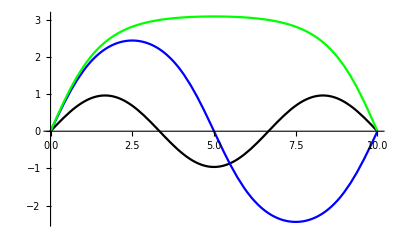

```mathematica
sols=Map[First[NDSolve[{x''[t]+Sin[x[t]]==0,x[0]==x[10]==0},x,t,Method->{"Shooting","StartingInitialConditions"->{x[0]==0,x'[0]==#}}]]&,{1.5,1.75,2}];
Plot[Evaluate[x[t]/.sols],{t,0,10},PlotStyle->{Black,Blue,Green}]
```

## Geodesisc numerically

Numerical derivative can be dangerous, set terms according to this :

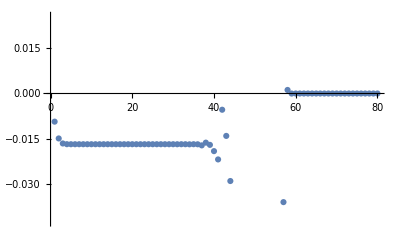

```mathematica
ListPlot@Table[ND[g[0.5,b],b,1,Terms->ter][[1,1]],{ter,80}]
terms=15;
```

```mathematica
geod[χ_,λ_]:=Module[{dg,gInv,gamma111,gamma112,gamma122,gamma211,gamma212,gamma222},
dg={ND[g[χ,l],l,λ,Terms->terms],ND[g[c,λ],c,χ,Terms->terms]};
gInv=Inverse[g[χ,λ]];
gamma111=1/2 Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}];
gamma112=1/2 Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}];
gamma122=1/2 Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}];
gamma211=1/2 Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}];
gamma212=1/2 Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}];
gamma222=1/2 Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}];
{χn''[τ]+gamma111 λn'[τ]^2+2gamma112 λn'[τ]χn'[τ]+gamma122 χn'[τ]χn'[τ],
λn''[τ]+gamma211 λn'[τ]^2+2gamma212 λn'[τ]χn'[τ]+gamma222 χn'[τ]χn'[τ]}
]
```

```mathematica
eqn={geod[χn[τ],λn[τ]][[1]]==0,geod[χn[τ],λn[τ]][[2]]==0};
dirichlet={χn[0]==0.1,χn[5]==2.3,λn[0]==0.1,λn[5]==0.3};
cauchy[xi_,la_]:={χn[0]==0.01,χn'[0]==xi,λn[0]==0.01,λn'[0]==la};
```

```mathematica
solMulti=Table[NDSolve[Join[eqn,cauchy[Cos[θ],Sin[θ]]],{χn,λn},{τ,0,5}, Method->{"EquationSimplification"->"Residual"}],{θ,0,π/2,π/5}];
```

NDSolve::ntdv: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

General::stop: Further output of NDSolve::ntdv will be suppressed during this calculation.

```mathematica
sol=NDSolve[Join[eqn,dirichlet],{χn,λn},{τ,0,5},Method->{"IndexReduction"->True}]
```

NDSolve::ntdv: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

```mathematica
g[1,1]
```

g[1,1]

## Test of Γ precision

```mathematica
Γ[λ_?NumericQ,χ_?NumericQ,q_?NumericQ,m_?NumericQ,n_?NumericQ]:=Module[{dg,derg,ggg},
dg={ND[g[χ,l],l,λ,Terms->terms],ND[g[c,λ],c,χ,Terms->20]};
derg=dg;
ggg[μ_,α_,β_]:=1/2 Sum[Inverse[g[λ,χ]][[μ,ν]](derg[[β,α,ν]]+derg[[α,ν,β]]-derg[[ν,β,α]]),{ν,1,2}];
ggg[q,m,n]
]
```

```mathematica
gTestF={{(1+8 χ^2)/(16+λ),8 λ χ},{8 λ χ,(8 λ^2)/(16+λ (32+17 λ))}};
gTest[λ_,χ_]:=gTestF;
ΓTest[λ_?NumericQ,χ_?NumericQ,q_?NumericQ,m_?NumericQ,n_?NumericQ]:=Module[{dg,derg,ggg},
dg={ND[gTest[l,χ],l,λ,Terms->terms],ND[gTest[λ,c],c,χ,Terms->20]};
derg=dg;
ggg[μ_,α_,β_]:=1/2 Sum[Inverse[gTest[λ,χ]][[μ,ν]](derg[[β,α,ν]]+derg[[α,ν,β]]-derg[[ν,β,α]]),{ν,1,2}];
ggg[q,m,n]
]
Metin[gTestF,{λ,χ}]
N@Christoffel[{{0},{0,0}}]/.{λ->1,χ->1}
ΓTest[1,1,1,1,1]
```

Metric Success

0.942166

0.

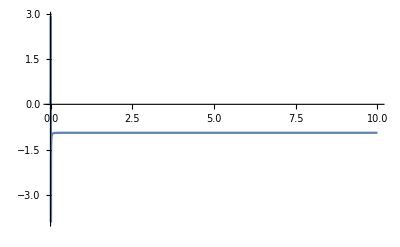

```mathematica
Plot[(ΓTest[λ,χ,1,1,1]-Christoffel[{{0},{0,0}}])/.{λ->1,χ->x},{x,0,10},PlotRange->Full]
```

```mathematica
(*dg[λ_,χ_]:={ND[g[l,χ],l,1,Terms->terms]/.l->λ,ND[g[λ,c],c,1,Terms->terms]/.c->χ}
gamma[μ_,α_,β_,λ_,χ_]:=1/2 Sum[Inverse[g[λ,χ]][[μ,ν]](dg[[β,α,ν]]+dg[[α,ν,β]]-dg[[ν,β,α]]),{ν,1,2}];*)
(*derg=dg[1,1]
Γ=1/2 Map[Inverse,derg](derg+Map[RotateLeft,derg]-RotateLeft[derg])*)
```

```mathematica
ChristoffelSymbol[g_,xx_]:=Block[{n,ig,res},n=Length[xx];ig=Inverse[g];res=Table[(1/2)*Sum[ig[[i,s]]*(-D[g[[j,k]],xx[[s]]]+D[g[[j,s]],xx[[k]]]+D[g[[s,k]],xx[[j]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}];Simplify[res]]
```

```mathematica
ChristoffelSymbol[g[2,1],{λ,χ}]
```